```mathematica
pts=Solve[y-(4x^2-x-3)/(√7)==0&&{x,y}∈Circle[{0,0},1],{x,y}]
```

{{x→1,y→0},{x→Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419,y→1/7 (-3 √7-√7 Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419+4 √7 (Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419)^2)},{x→Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144,y→1/7 (-3 √7-√7 Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144+4 √7 (Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144)^2)},{x→Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336,y→1/7 (-3 √7-√7 Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336+4 √7 (Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336)^2)}}

```mathematica
pts/.Rule->List
```

{{{x,1},{y,0}},{{x,Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419},{y,1/7 (-3 √7-√7 Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419+4 √7 (Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419)^2)}},{{x,Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144},{y,1/7 (-3 √7-√7 Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144+4 √7 (Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144)^2)}},{{x,Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336},{y,1/7 (-3 √7-√7 Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336+4 √7 (Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336)^2)}}}

```mathematica
pts1=Solve[y+(4x^2-x-3)/(√7)==0&&{x,y}∈Circle[{0,0},1],{x,y}]
```

{{x→1,y→0},{x→Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419,y→1/7 (3 √7+√7 Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419-4 √7 (Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419)^2)},{x→Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144,y→1/7 (3 √7+√7 Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144-4 √7 (Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144)^2)},{x→Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336,y→1/7 (3 √7+√7 Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336-4 √7 (Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336)^2)}}

```mathematica
points=Union[pts,pts1]
```

{{x→1,y→0},{x→Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419,y→1/7 (3 √7+√7 Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419-4 √7 (Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419)^2)},{x→Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419,y→1/7 (-3 √7-√7 Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419+4 √7 (Root-0.901Root[-1-4 #1+4 #1^2+8 #1^3&,1]-0.900968867902419)^2)},{x→Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144,y→1/7 (3 √7+√7 Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144-4 √7 (Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144)^2)},{x→Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144,y→1/7 (-3 √7-√7 Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144+4 √7 (Root-0.223Root[-1-4 #1+4 #1^2+8 #1^3&,2]-0.2225209339563144)^2)},{x→Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336,y→1/7 (3 √7+√7 Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336-4 √7 (Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336)^2)},{x→Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336,y→1/7 (-3 √7-√7 Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336+4 √7 (Root0.623Root[-1-4 #1+4 #1^2+8 #1^3&,3]0.6234898018587336)^2)}}

```mathematica
pts3=Table[{Cos[2n π/7],Sin[2 n π/7]},{n,0,6}];
```

```mathematica
parabola=ContourPlot[{x^2+y^2==1,y==(4x^2-x-3)/(√7),y==-(4x^2-x-3)/(√7)},{x,-2,1.6},{y,-2,2},Axes->True,Frame->False,Ticks->{{-1,0.5,1,0,-0.5},{-0.5,-1,0,1,0.5}},AspectRatio->Automatic,PlotLegends->"Expressions"];
```

```mathematica
intersections={Red,PointSize[Medium],Point[{x,y}/.points]};
```

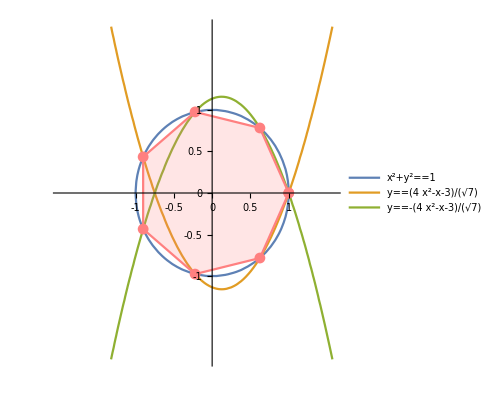

```mathematica
Show[{parabola,Graphics[intersections],ListLinePlot[pts3[[Last@FindShortestTour[pts3]]],Mesh->All,PlotStyle->Pink,AspectRatio->Automatic,Filling->Axis]}]
```